```mathematica
a={1,0};
b={1/2,Sqrt[3]/2};
```

```mathematica
tau={a,b,-a,-b,b-a,a-b}
```

{{1,0},{1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{-1/2,(√3)/2},{1/2,-(√3)/2}}

```mathematica
k={kx,ky}
```

{kx,ky}

```mathematica
E4s[kx_,ky_]:=10-Sum[Exp[I k.tau[[i]]],{i,1,6}]//FullSimplify
```

```mathematica
Plot3D[E4s[kx,ky],{kx,ky}∈Region[ RegularPolygon[4Pi/3,6]],PlotPoints->100,Axes->False,AspectRatio->1]
```

-Graphics3D-

```mathematica
ContourPlot[E4s[kx,ky],{kx,ky}∈Region[ RegularPolygon[6Pi/3,6]],ColorFunction->"SunsetColors",Contours->40,PlotPoints->150,Axes->False,LabelStyle->Opacity[0]]
```

-Graphics-

```mathematica
E4s[kx,ky]//FullSimplify
```

-2 (Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2])

```mathematica
6*Sqrt[3]a^2/4
```

```mathematica
6*Sqrt[3](4Pi/3)^2/4
```

(8 π^2)/(√3)

```mathematica
Solve[6*Sqrt[3]xx^2/4==4Pi^2/Sqrt[3],xx]
```

{{xx→-(2 √2 π)/3},{xx→(2 √2 π)/3}}

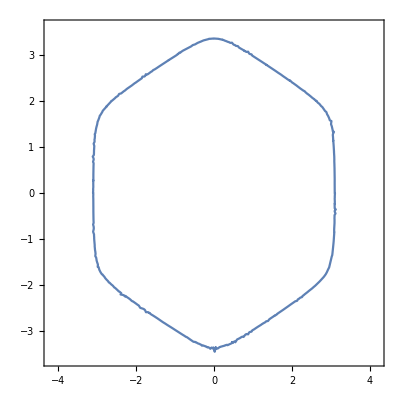

```mathematica
ContourPlot[E4s[kx,ky]==11.9,{kx,ky}∈Region[ RegularPolygon[4Pi/3,6]]]
```